# Série 4 - Tópicos Avançados de Física Computacional Nuno Teixeira n.ba75494

```mathematica
ClearAll["Global`*"]
```

## Pergunta 1)

## Resposta 1a)

```mathematica
Parametros={R->0.9,A->(16 π)/1.48^2}
```

{R→0.9,A→22.9481}

### Potencial dado

```mathematica
V[r]=-4/r Erf[r/R]+A(√π R)^-3 ⅇ^(-r^2/R^2)
```

(A ⅇ^(-r^2/R^2))/(π^(3/2) R^3)-(4 Erf[r/R])/r

## Transformada de Fourier

```mathematica
Pot[r]=V[r]/.Parametros
```

5.6532 ⅇ^(-1.23457 r^2)-(4 Erf[1.11111 r])/r

```mathematica
FTV[k]=(2 π)^(3/2)Integrate[Pot[r] BesselJ[1/2, k r] r^(3/2),{r,0,∞}]/k^(1/2)
```

(2 √2 ⅇ^(-0.2025 k^2) (-3.19154+1.45706 k^2) π^(3/2))/k^2

(2 √2 ⅇ^(-0.2025 k^2) (-3.19154+1.45706 k^2) π^(3/2))/k^2

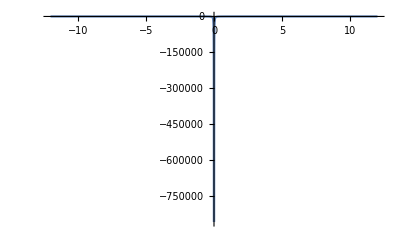

```mathematica
(*V[r]*)
FTV[k]
Plot[FTV[k],{k,-12,12},PlotRange->All]

(*Plot[FTV[k],{k,0,2},PlotRange->All]*)
```

Com isto, sabendo que estamos na aproximação thomas-fermi, a permitividade ϵ(q) é dada por,

```mathematica
vFermi=0.35
```

0.35

```mathematica
ϵ[k]=1+vFermi^2/k^2;
```

O nosso potencial perturbado é dado por auto-consistência
 	U=V/(ϵ(q))

```mathematica
FTU[k]=FTV[k]/ϵ[k];
```

```mathematica
Klim=1000
```

1000

```mathematica
(*interpol1 =Interpolation[Table[{k ,FTU[k]BesselJ[1/2,k r] k^(3/2) },{k,0,Klim,0.1}]]*)
```

```mathematica
U[r_?NumericQ]:=NIntegrate[(FTU[k]BesselJ[1/2,k r] k^(3/2))/r^(1/2),{k,0,Klim}]
```

```mathematica
rlim=10
```

10

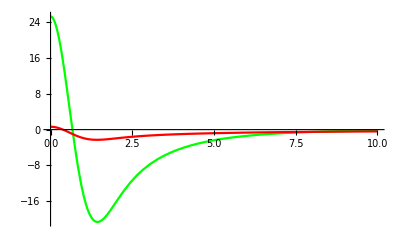

```mathematica
a=Plot[U[r],{r,0,rlim},PlotStyle->Green,PlotLegends->Placed[PointLegend[{Green},{"After screening"}],{Right,Top}]];
b=Plot[Pot[r],{r,0,rlim},PlotStyle->Red,PlotLegends->Placed[PointLegend[{Red},{"Before screening"}],{Right,Top}]];
Show[a,b,PlotRange->All]
```

```mathematica
(*lista de energias tentadas-1, 0.1, 0.01,0.001,100,*)
(*valores relevantes de energia*)
(*E=-5, E muito elevada - baixar*)
(*E=-7.5 muito elevada - baixar*)
(*E=-10 muito baixa - subir*)
(*E=-8.5 muito baixa - subir*)
(*E=-8 muito baixa - subir*)
(*En=-7.65 muito baixa -subir*)
(*E=-7.645 muito elevada -baixar*)
(*E=-7.6465 muito elevada -baixar*)
(*En=-7.6475 muito baixa -subir*)
(*En=-7.6455 muito baixa -subir*)
(*En=-7.6451 bom valor mas não é a energia que eu quero, esta é a energia do nivel 3*)
(*E=-17.37979*)
```

```mathematica
(*Subscript[Energia, n=1,l=0]=-11.8071596765 u.a.*)
```

-10.9975

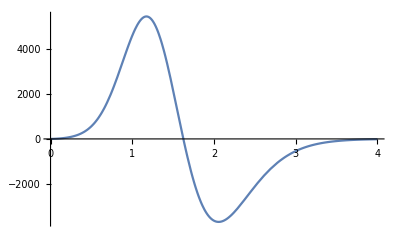

```mathematica
(*En=-10.9972230;*)
En=-10.99747315
l=1;
(*Sol=NDSolve[{-(1/r R'[r]+1/2 R''[r])+(l(l+1))/r^2 R[r]+U[r]  R[r]==En R[r],R[0.000001]==0,R'[0.000001]==1},R[r],{r,0.000001,10}];*)
Sol=NDSolve[{-(1/r R'[r]+1/2 R''[r])+(l(l+1))/r^2 R[r]+U[r]  R[r]==En R[r],R[0.000001]==0,R'[0.000001]==1},R[r],{r,0.000001,30}];
R1[r_]:=R[r]/.Sol;

Plot[R1[r],{r,0.000001,4},PlotRange->All]
```

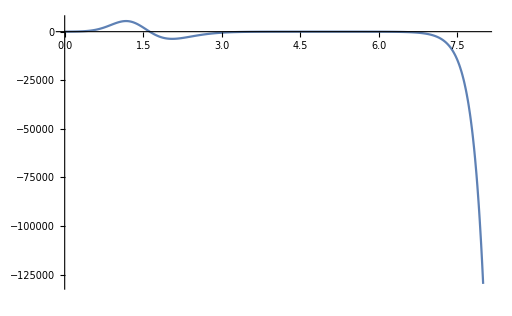

```mathematica
Plot[R1[r],{r,0.000001,8},PlotRange->All]
```

```mathematica
revised1[k1,k2,k11,k22]
```

revised1[k1,k2,k11,k22]

```mathematica
revised1[1,2,3,4]
```

revised1[1,2,3,4]